```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 101/100;
uOuterDomains=2;
uOuterNodes=24;
uInnerNodes=12;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,0.555,1.01}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

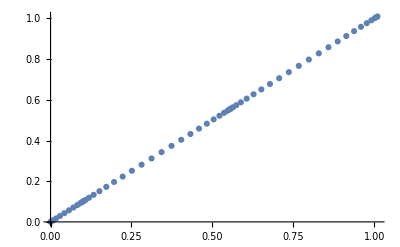

```mathematica
ListPlot[Transpose[{uValues,uValues}]]
```

```mathematica
uValues
```

{0,0.00202535131927513050548159714668361504687725757889190224777524705,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1,0.1021189472767347538421215265781131338306501857640274511247018283,0.1084363171283756603840366315975881731467333007883136850876891717,0.1188344289075094384405342605878224751854580758219064506794060735,0.1331195854656738542952809465523179429891128430614119641786574147,0.1510256813647444938981495200044303562537930788513104475280988812,0.1722191599177561961460427084277470184825296527163733839093903902,0.1963052267188677253653865173767909825448056290177239702524232509,0.2228352039161628913255415146430084665105717287489801769244981327,0.2513148882311006504295288213821049891670617246586546663306526825,0.2812137570305258128027484657309909079080428407825029497985611582,0.3119748509595373529779296210223905720552216719839591739835135512,0.3430251490404626470220703789776094279447783280160408260164864488,0.3737862429694741871972515342690090920919571592174970502014388418,0.4036851117688993495704711786178950108329382753413453336693473175,0.4321647960838371086744584853569915334894282712510198230755018673,0.4586947732811322746346134826232090174551943709822760297475767491,0.4827808400822438038539572915722529815174703472836266160906096098,0.5039743186352555061018504799955696437462069211486895524719011188,0.5218804145343261457047190534476820570108871569385880358213425853,0.5361655710924905615594657394121775248145419241780935493205939265,0.5465636828716243396159633684024118268532666992116863149123108283,0.5528810527232652461578784734218868661693498142359725488752981717,0.555,0.5571189472767347538421215265781131338306501857640274511247018283,0.5634363171283756603840366315975881731467333007883136850876891717,0.5738344289075094384405342605878224751854580758219064506794060735,0.5881195854656738542952809465523179429891128430614119641786574147,0.6060256813647444938981495200044303562537930788513104475280988812,0.6272191599177561961460427084277470184825296527163733839093903902,0.6513052267188677253653865173767909825448056290177239702524232509,0.6778352039161628913255415146430084665105717287489801769244981327,0.7063148882311006504295288213821049891670617246586546663306526825,0.7362137570305258128027484657309909079080428407825029497985611582,0.7669748509595373529779296210223905720552216719839591739835135512,0.7980251490404626470220703789776094279447783280160408260164864488,0.8287862429694741871972515342690090920919571592174970502014388418,0.8586851117688993495704711786178950108329382753413453336693473175,0.8871647960838371086744584853569915334894282712510198230755018673,0.9136947732811322746346134826232090174551943709822760297475767491,0.9377808400822438038539572915722529815174703472836266160906096098,0.9589743186352555061018504799955696437462069211486895524719011188,0.9768804145343261457047190534476820570108871569385880358213425853,0.9911655710924905615594657394121775248145419241780935493205939265,1.001563682871624339615963368402411826853266699211686314912310828,1.007881052723265246157878473421886866169349814235972548875298172,1.01}

#### x Domain

```mathematica
xMin=-5;
xMax=5;
xNodes=150;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-5,-74/15,-73/15,-24/5,-71/15,-14/3,-23/5,-68/15,-67/15,-22/5,-13/3,-64/15,-21/5,-62/15,-61/15,-4,-59/15,-58/15,-19/5,-56/15,-11/3,-18/5,-53/15,-52/15,-17/5,-10/3,-49/15,-16/5,-47/15,-46/15,-3,-44/15,-43/15,-14/5,-41/15,-8/3,-13/5,-38/15,-37/15,-12/5,-7/3,-34/15,-11/5,-32/15,-31/15,-2,-29/15,-28/15,-9/5,-26/15,-5/3,-8/5,-23/15,-22/15,-7/5,-4/3,-19/15,-6/5,-17/15,-16/15,-1,-14/15,-13/15,-4/5,-11/15,-2/3,-3/5,-8/15,-7/15,-2/5,-1/3,-4/15,-1/5,-2/15,-1/15,0,1/15,2/15,1/5,4/15,1/3,2/5,7/15,8/15,3/5,2/3,11/15,4/5,13/15,14/15,1,16/15,17/15,6/5,19/15,4/3,7/5,22/15,23/15,8/5,5/3,26/15,9/5,28/15,29/15,2,31/15,32/15,11/5,34/15,7/3,12/5,37/15,38/15,13/5,8/3,41/15,14/5,43/15,44/15,3,46/15,47/15,16/5,49/15,10/3,17/5,52/15,53/15,18/5,11/3,56/15,19/5,58/15,59/15,4,61/15,62/15,21/5,64/15,13/3,22/5,67/15,68/15,23/5,14/3,71/15,24/5,73/15,74/15}

```mathematica
Deltax^4//N
```

0.0000197531

#### y Domain

```mathematica
yMin=-5;
yMax=5;
yNodes=xNodes;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues
```

{-5,-74/15,-73/15,-24/5,-71/15,-14/3,-23/5,-68/15,-67/15,-22/5,-13/3,-64/15,-21/5,-62/15,-61/15,-4,-59/15,-58/15,-19/5,-56/15,-11/3,-18/5,-53/15,-52/15,-17/5,-10/3,-49/15,-16/5,-47/15,-46/15,-3,-44/15,-43/15,-14/5,-41/15,-8/3,-13/5,-38/15,-37/15,-12/5,-7/3,-34/15,-11/5,-32/15,-31/15,-2,-29/15,-28/15,-9/5,-26/15,-5/3,-8/5,-23/15,-22/15,-7/5,-4/3,-19/15,-6/5,-17/15,-16/15,-1,-14/15,-13/15,-4/5,-11/15,-2/3,-3/5,-8/15,-7/15,-2/5,-1/3,-4/15,-1/5,-2/15,-1/15,0,1/15,2/15,1/5,4/15,1/3,2/5,7/15,8/15,3/5,2/3,11/15,4/5,13/15,14/15,1,16/15,17/15,6/5,19/15,4/3,7/5,22/15,23/15,8/5,5/3,26/15,9/5,28/15,29/15,2,31/15,32/15,11/5,34/15,7/3,12/5,37/15,38/15,13/5,8/3,41/15,14/5,43/15,44/15,3,46/15,47/15,16/5,49/15,10/3,17/5,52/15,53/15,18/5,11/3,56/15,19/5,58/15,59/15,4,61/15,62/15,21/5,64/15,13/3,22/5,67/15,68/15,23/5,14/3,71/15,24/5,73/15,74/15}

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{58,150,150,3}

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### ρ

```mathematica
modesTot=4;
```

```mathematica
RandomCoefficients=Table[(Random[])/5,{i,1,modesTot}]
```

{0.1735,0.0174631,0.0841255,0.194007}

```mathematica
RandomCoefficients2=Table[2Pi(Random[]),{i,1,modesTot}]
```

{4.48786,0.183436,2.90904,0.963899}

```mathematica
RandomDirections=Table[{Cos[RandomCoefficients2[[i]]],Sin[RandomCoefficients2[[i]]]}(*{Random[],Random[]}*)//Normalize,{i,1,modesTot}]
```

{{-0.222652,-0.974898},{0.983223,0.182409},{-0.97308,0.230466},{0.570321,0.821422}}

```mathematica
RandomDirections2=Table[{Cos[RandomCoefficients2[[i]]],Sin[RandomCoefficients2[[i]]]}(*{Random[],Random[]}*)//Normalize,{i,1,modesTot}]
```

{{-0.222652,-0.974898},{0.983223,0.182409},{-0.97308,0.230466},{0.570321,0.821422}}

```mathematica
Norm[RandomCoefficients]
```

0.274086

```mathematica
RandomFactor[{x_,y_}]=(Sum[RandomCoefficients[[i]]Cos[(( i+1) 2Pi x/(xMax-xMin)-(xMax-xMin)/(2Pi( i+1))(RandomReal[]-0.5))]Sin[(( i+1)2Pi y/(xMax-xMin)-(yMax-yMin)/(2Pi( i+1))(RandomReal[]-0.5))],{i,1,modesTot}]);
```

```mathematica
RandomFactor2[{x_,y_}]=0(Sum[RandomCoefficients2[[i]]Cos[(2i Pi (({x,y}.RandomDirections2[[i]])/(xMax-xMin))-(xMax-xMin)(RandomReal[]-0.5))](*+Random[]Sin[(i Pi (y-10(RandomReal[]-0.5)))/(xMax-xMin)]Cos[(i Pi (x-10(RandomReal[]-0.5)))/(yMax-yMin)]*),{i,3,4}(*,{j,7,8}*)](*+Sum[1/100(+Random[]Sin[(i Pi y)/(yMax-yMin)+1.34]),{i,9,10}]*)(*+Sum[1/100(+Random[]Sin[(i Pi x)/(xMax-xMin)+0.23]),{i,9,10}(*,{j,7,8}*)]+Sum[1/100(+Random[]Cos[(i Pi y)/(yMax-yMin)]),{i,9,10}]*))
```

0

#### Proper random function

```mathematica
δuxToInt[x_,y_]:=Table[{{x,y},(Random[]-0.5)/20(*Cos[qx y]+RandomFactor[x,y]*)},{x,xMin,xMax,0.1},{y,yMin,yMax,0.1}];
```

```mathematica
Intδux=Interpolation[δuxToInt[x,y]//Flatten[#,1]&]
```

InterpolatingFunction[…]

```mathematica
XYGrid=Flatten[MyGrid[[1,;;,;;,2;;]],1];
RFTable1=RandomFactor(*[{x,y}]*)/@XYGrid;
(*XYGrid//Dimensions
RFTable//Dimensions*)
```

```mathematica
DataToInt=Table[{{XYGrid[[i,1]],XYGrid[[i,2]]},RFTable1[[i]]},{i,1,RFTable1//Length}];
```

```mathematica
Borders=Join[Select[DataToInt,#[[1,1]]==-5 &],Select[DataToInt,#[[1,2]]==-5 &]]/.-5->5;
BordersData=Join[Table[{{Borders[[n,1,1]],Borders[[n,1,2]]},Borders[[n,2]]},{n,1,Borders//Length}],{{{5,-5},DataToInt[[1,2]]},{{-5,5},DataToInt[[1,2]]}}];
```

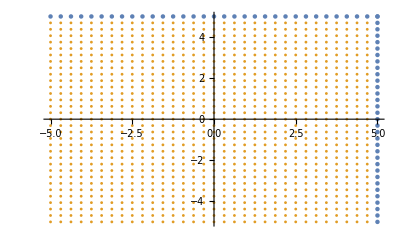

```mathematica
ListPlot[{BordersData[[;;,1]],DataToInt[[;;,1]](*,{{-5,5},{5,-5}}*)},PlotStyle->{PointSize[0.008],PointSize[0.005]}]
```

```mathematica
RFT=Interpolation[Join[DataToInt,BordersData[[2;;]]],Method->"Spline"]
```

InterpolatingFunction[…]

#### Boosting

```mathematica
ContourPlot[1/100 RandomFactor[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"MintColors",MaxRecursion->3(*,PlotPoints->20*)]
```

-Graphics-

```mathematica
ClearAll[u1d,u0d,u2d]
qx=(4Pi)/(xMax-xMin);
qy=Pi/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)
OriginalPertEn=45962;
NormCoeff=Abs[A/.Solve[0.99==1-1/A^2 OriginalPertEn,A][[1]]];//Quiet
(*NormCoeff=100;*)
u1d[x_,y_]:=(*0.1*)0Cos[qx y] (*+(*RFT[x,y]*)1/100RandomFactor[{x,y}]*);
u2d[x_,y_]:=0(*RandomFactor2[{x,y}]*);
(*Translate from energy to radius*)
b=1-(OriginalPertEn/NormCoeff^2)^(1/4)
```

0.683772

```mathematica
51.173708250988994/100^2
```

0.00511737

```mathematica
E^(I 2 Pi/L y)//Re
```

Re[ⅇ^((2 ⅈ π y)/L)]

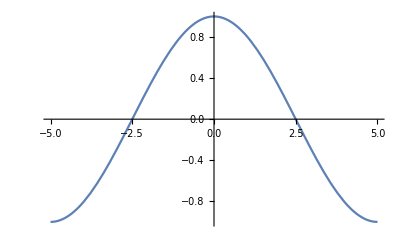

```mathematica
Plot[Cos[2 Pi/L y]/.L->10,{y,-5,5}]
```

The horizon (b) has to be shifted by the energy computed in the masterscalar notebook (0.5013868846238644`). also, the 20 squared factor comes from the normalization factor used some paragraphs down.

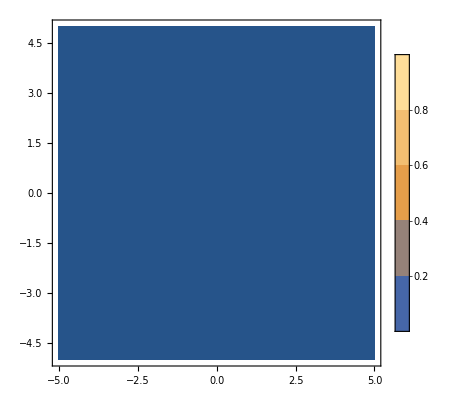

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->4*)(*,PlotPoints->20*)]
```

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[1,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ//N
```

Function[{ρ,x,y},1./ρ+C[1][x,y]]

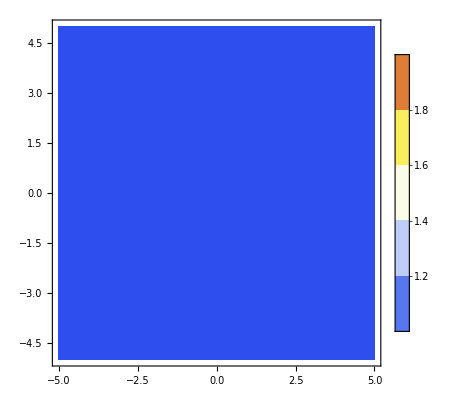

```mathematica
ContourPlot[rofρ[1,x,y]/.C[1][x,y]->0,{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->5(*,PlotPoints->20*)]
```

```mathematica
result={c2->-0.24762128391507528657906785005173909625976685242963218096521979878218387200135`55.+3.67912767260729585436798865243943894371221895858216870655358535718925903341104`55. ⅈ,vzx->3.68196494112293402558482142910039546458637786430300364449928320381702930729343`55.+6.9431822550987137573184657263720294903219035390434438024837497761322166925203`55. ⅈ,ω->3.16547441328186133648889938297347926915113759362323018079864039871832116007918`55.-2.73240323018858175660950845702563645683965512319086455084589837696965044454512`55. ⅈ};
```

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]
```

Function[{ρs,xs,ys},1/rofρ⟦2⟧/.c1Rule⟦1⟧/.ξ→Function[{t,x,y},0]/.ρ→ρs/.x→xs/.y→ys]

Horizon location

```mathematica
Minimize[uofρ[b,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
Maximize[uofρ[b,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
```

0.683772

0.683772

```mathematica
Plot3D[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,(*PlotRange->All,*)(*MaxRecursion->4,*)ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

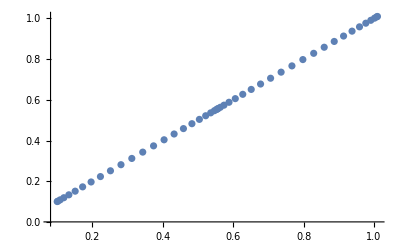

```mathematica
ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
```

{58,150,150,3}

```mathematica
ρofuValues=ParallelTable[ρofu[MyGrid[[i,j,k]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{152.213,Null}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.142364,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.021225,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{10.225,Null}

#### Perturbations

```mathematica
(*result={c2->-0.24762128391507528657906785005173909625976685242963218096521979878218387200135`55.+3.67912767260729585436798865243943894371221895858216870655358535718925903341104`55. ⅈ,vzx->3.68196494112293402558482142910039546458637786430300364449928320381702930729343`55.+6.9431822550987137573184657263720294903219035390434438024837497761322166925203`55. ⅈ,ω->3.16547441328186133648889938297347926915113759362323018079864039871832116007918`55.-2.73240323018858175660950845702563645683965512319086455084589837696965044454512`55. ⅈ};*)
```

```mathematica
htxFunction[z_,x3_]:=1/NormCoeff ⅇ^(ⅈ (k x3-v ω)) ((*ϵ*)1)/2(Piecewise[{{InterpolatingFunction[…][z], z<1/2}, {InterpolatingFunction[…][z], z≥1/2}, {0, True}}])/.k->2 Pi/L/.v->0(*/.ϵ->1/20*)/.k->2 Pi/L/.L->yMax-yMin/.result;
hxyFunction[z_,x3_]:=1/NormCoeff ⅇ^(ⅈ (k x3-v ω)) ((*ϵ*)1)/2(Piecewise[{{InterpolatingFunction[…][z], z<1/2}, {InterpolatingFunction[…][z], z≥1/2}, {0, True}}])/.v->0(*/.ϵ->1/20*)/.k->2 Pi/L/.L->yMax-yMin/.result;
```

```mathematica
htxFunction[0,0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-8.70309×10^-28-1.64113×10^-27 ⅈ

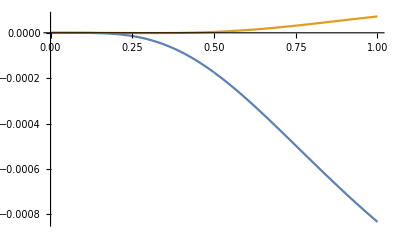

```mathematica
Plot[{hxyFunction[z,2]//Re,htxFunction[z,2]//Re},{z,0,1},PlotRange->All]
```

```mathematica
Plot3D[hxyFunction[z,y]//Re,{z,0,1},{y,-5,5},PlotRange->All]
```

-Graphics3D-

Here we need to consider the definition of the perturbation in terms of the radial profile. In the nb where we compute the radial profile, we have h = e^(ikx_3-iωv)/(2 u^2)h(z),

```mathematica
Parametricgxy[u_,y_]:=hxyFunction[u,y](*/Normaxy*)//Re;
Parametricgtx[u_,y_]:=htxFunction[u,y](*/Normaxy*)//Re;
```

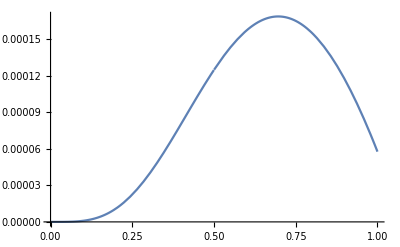

```mathematica
Plot[Parametricgxy[u,yValues[[1]]],{u,0,1.00},PlotRange->All]
```

The third equations has to include the complete perturbation as “a”

```mathematica
BulkFunctions=Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==u^-2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-a^2)^(1/6))/u,Gin→Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in→0,B2in→-Log[(1-a^2)^(1/6)]/u^4}

```mathematica
{S->-((1-a^2)^(1/6))/u,Gin->Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in->0,B2in->-Log[(1-a^2)^(1/6)]/u^4}//TeXForm
```

\left\{S\to -\frac{\sqrt[6]{1-a^2}}{u},\text{Gin}\to \frac{\log \left(\frac{-\sqrt{1-a^2} a-\sqrt{1-a^2}}{a^2-1}\right)}{u^4},\text{B1in}\to
   0,\text{B2in}\to -\frac{\log \left(\sqrt[6]{1-a^2}\right)}{u^4}\right\}

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u^2 a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ,x,y]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,2}]&
```

1/ρ^2+(2. ξ[t,x,y]+2. C[1][x,y])/ρ+(ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2-2 ξ^(1,0,0)[t,x,y])+1. a3[t,0,x,y] ρ^2+O[ρ]^3

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b ρ)^4(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-0.218598 ρ^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  C[1][x,y]]//Flatten
```

{C[1][x,y]→-1. ξ[t,x,y]}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
Coefficient[AToMatch,ρ^2]
```

-0.218598

```mathematica
Coefficient[AExpOfρ,ρ^2]
```

1. a3[t,0,x,y]

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ^2]==Coefficient[AExpOfρ,ρ^2],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-0.218598}

From Chasler paper a3 should be

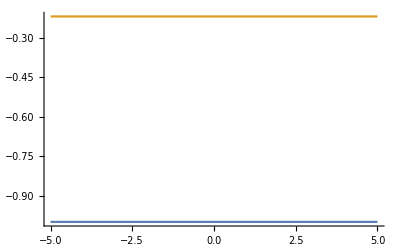

```mathematica
Plot[{-1/2(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,-5,5}]
```

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
a3Data[[13,1]]
```

-0.218598

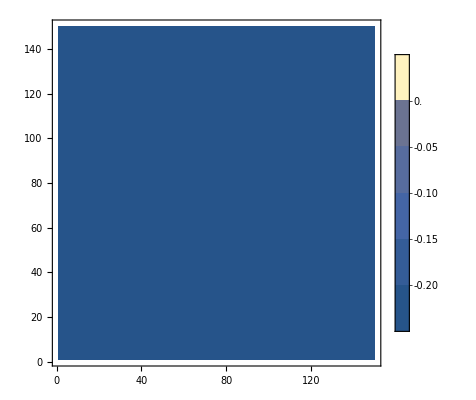

```mathematica
ListContourPlot[a3Data,PlotLegends->Automatic]
```

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

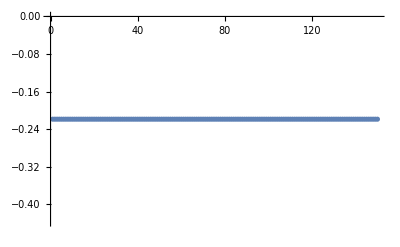

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"][[1,1]]]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u^2 f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->(*rofρ[ρ,x,y]^-1*)z(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{z,0,4}]&
```

ξ^(0,1,0)[t,x,y]+f1[t,0,y] z^2+f1^(0,1,0)[t,0,y] z^3+1/2 f1^(0,2,0)[t,0,y] z^4+O[z]^5

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
FToMatch=1/NormCoeff vzx z^4 E^(I k y)/(2 z^2)/.v->0/.k->2 Pi/L/.result//Re//Simplify(*-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2u0d[x,y] u1d[x,y];*)
```

Re[(0.000858717+0.00161931 ⅈ) ⅇ^((2 ⅈ π y)/L) z^2]

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,z^2]==Coefficient[FExpOfρ,z^2],f1[t,z,y]]//Simplify
```

{}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

Part::partw: Part 1 of {} does not exist.

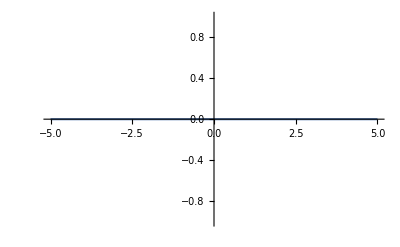

```mathematica
Plot[{-u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{}

```mathematica
I
```

ⅈ

ξ can’t depend on x!

Export fx initial data

The source term goes to zero. The Vev is the first term and it is

```mathematica
1/NormCoeff vzx z^4 E^(I k y)/(2 z^2)/.v->0/.k->2 Pi/L/.result//Re//Simplify
```

Re[(0.000858717+0.00161931 ⅈ) ⅇ^((2 ⅈ π y)/L) z^2]

```mathematica
rma
```

rma

```mathematica
NormCoeff
```

2143.87

```mathematica
fxData=Table[1/2 1/NormCoeff vzx E^(I k y)/.x->xValues[[i]]/.y->yValues[[j]]/.k->2 Pi/L/.L->10/.result//Re,{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fxData;
```

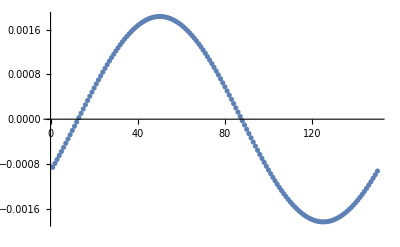

```mathematica
fxData[[1]]//ListPlot[#,PlotRange->All]&
```

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5

```mathematica
fxAttributesAndData[[1,2]]
```

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

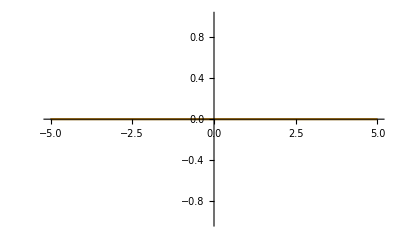

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyData=Table[(f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{150,150}

```mathematica
ListPlot3D[fyData]
```

-Graphics3D-

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### Bulk Functions

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialBAnalytic[u,x,y]
```

0.

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1]],0}]//Normal](*(1+ (RandomReal[]-0.5)/100)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.299385,Null}

```mathematica
InitialB=ParallelTable[N[-1/2 Log[(1+(b ρofuValues[[ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/100)*),{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

-3
Power::infy: Infinite expression 0   encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

-3
Power::infy: Infinite expression 0   encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

-3
Power::infy: Infinite expression 0   encountered.

General::stop: Further output of Power::infy
     will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet
     will be suppressed during this calculation.

{83.0259,Null}

```mathematica
InitialB//Dimensions
```

{58,150,150}

```mathematica
(*Table[InitialB[[1,i,j]]=-u1d[xValues[[i]],yValues[[j]]]^2/2,{i,1,xValues//Length},{j,1,yValues//Length}];*)
```

```mathematica
(*ListContourPlot[InitialB[[1]],PlotLegends->Automatic]*)
```

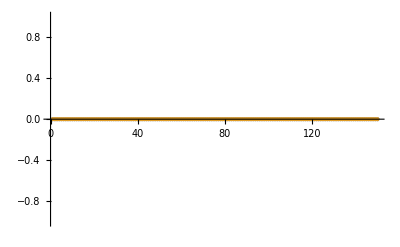

```mathematica
ListPlot[{InitialB[[1,1,;;]],Table[-u1d[xValues[[1]],yValues[[i]]]^2/2(*-InitialB[[1,1,i]]*),{i,1,yValues//Length}]}(*,Joined->True*)(*,PlotStyle->{Dashed,Dotted}*)]
```

```mathematica
(*phiFunc=InterpolatingFunction[…]*)
```

```mathematica
(*phi=Table[phiFunc[uValues[[i]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];*)
```

```mathematica
ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000489,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000024,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

#### B2 Function

```mathematica
BulkFunctions
```

BulkFunctions

```mathematica
(*InitialB2=ParallelTable[N[-Log[(1-4 a^2 u^8)^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming*)
InitialB2=ParallelTable[N[-Log[(1- a^2 )^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]],yValues[[yi]]]/.u->uValues[[ui]]/.y->yValues[[yi]](*//Re*),$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

{44.462,Null}

```mathematica
Parametricgxy[uValues[[10]],yValues[[10]]]
```

6.0579×10^-7

```mathematica
InitialB2//Dimensions
```

{58,150,150}

```mathematica
uValues//Length
```

58

```mathematica
InitialB2[[2]]
```

```mathematica
IntFuncts=Table[Interpolation[{uValues[[;;-4]],InitialB2[[;;-4,1,j]]}//Transpose],{j,1,yValues//Length}];
```

```mathematica
Table[InitialB2[[u,i,j]]=IntFuncts[[j]][uValues[[u]]],{u,-4,-1},{i,1,xValues//Length},{j,1,yValues//Length}];
```

InterpolatingFunction::dmval: Input value {1.001563682871624339615963368402411826853266699211686314912310828} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Max[InitialB2]
```

1.31235×10^-7

```mathematica
InitialB2uzero=ParallelTable[0,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.071748,Null}

```mathematica
InitialB2[[1]]=InitialB2uzero;
```

```mathematica
InitialB2[[;;,;;,;;]]//Flatten//Im//Norm
```

0

```mathematica
ExportDataB2=Join[{InitialB2(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB2(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000443,Null}

```mathematica
ExportAttributesB2=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataB2=Table[ExportAttributesB2[[i]]->ExportDataB2[[i]],{i,1,ExportAttributesB2//Length}];//AbsoluteTiming
```

{1.88844,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5",AttributesAndDataB2,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5

#### G Function

```mathematica
BulkFunctions
```

{S→-((1-a^2)^(1/6))/u,Gin→Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in→0,B2in→-Log[(1-a^2)^(1/6)]/u^4}

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->((*ⅇ^(ⅈ k x3)*)Cos[k x3])/2 vzx u^4/.k->2 Pi/L,{u,0,10}](*/.result*)(*/.u->0*)(*//Normal*)
```

1/2 vzx Cos[(2 π x3)/L]+1/24 vzx^3 Cos[(2 π x3)/L]^3 u^8+O[u]^11

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==u^-2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-a^2)^(1/6))/u,Gin→Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in→0,B2in→-Log[(1-a^2)^(1/6)]/u^4}

```mathematica
InitialG=ParallelTable[N[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->Parametricgxy[uValues[[ui]],yValues[[yi]]]/.u->uValues[[ui]](*/.y->yValues[[yi]]*)(*,$MinPrecision*)],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {0} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.007881052723265246157878473421886866169349814235972548875298
      172} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {1.001563682871624339615963368402411826853266699211686314912310
      828} lies outside the range of data in the interpolating function.
     Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

{56.7793,Null}

InterpolatingFunctio/ListPlotn::dmval :  Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->-(u^4 ω vzx)/k E^(I k y)/(2NormCoefff)(*/.result*),{u,0,2}]
```

-(ⅇ^(ⅈ k y) vzx ω)/(2 (k NormCoefff))+O[u]^3

```mathematica
InitialG1=ParallelTable[-(vzx ω E^(I k yValues[[j]]))/(2 NormCoeff k)/.result/.k->2 Pi/(yMax-yMin)//Re,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.21684,Null}

```mathematica
InitialG[[1]]=InitialG1;
```

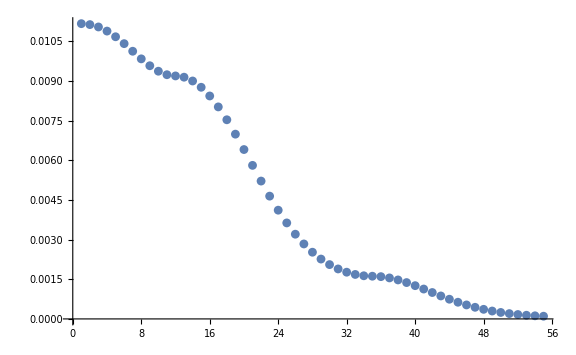

```mathematica
ListPlot[InitialG[[;;,1,2]](*,Joined->True*),PlotRange->All,ImageSize->Large]
```

```mathematica
IntFunctsG=Table[Interpolation[{uValues[[;;-4]],InitialG[[;;-4,1,j]]}//Transpose],{j,1,yValues//Length}];
```

```mathematica
Table[InitialG[[u,i,j]]=IntFunctsG[[j]][uValues[[u]]],{u,-4,-1},{i,1,xValues//Length},{j,1,yValues//Length}];
```

InterpolatingFunction::dmval: Input value {1.001563682871624339615963368402411826853266699211686314912310828} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Max[InitialG]
```

0.0121984

```mathematica
ListPlot3D[InitialG[[-1]]]
```

-Graphics3D-

```mathematica
ExportDataG=Join[{InitialG(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialG(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.00065,Null}

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->ExportDataG[[i]],{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{4.87764,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5